# Little Tests

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
<<"pyramidalStereoAll`"

methods={"","OverConstrained","SemiConstrained","Constrained","ConstrainedInitialSign","ConstrainedNewMethod","ConstrainedPickierFunction"};
Do[
Get["pyramidalCyclope1D"<>met<>"`"]
,{met,methods}]
```

```mathematica
(* Declare path for SINTEL Data depending on user*)

baseAEREAL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Aereal",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
reduce=2;
path1=FileNameJoin[{baseAEREAL,"Aereal1.png"}];
path2=FileNameJoin[{baseAEREAL,"Aereal2.png"}];
pathResult=FileNameJoin[{baseAEREAL,"AerealResult.png"}];

rgb2d[{r_,g_,b_}]:=r*4+g/64;
clean[img_]:=Image[ImageData[img]];

reduire[img_,1]:=img;
reduire[img_,factor_]:=ImageResize[img,ImageDimensions[img]/factor];

ia=reduire[ColorConvert[clean@Import[path1],"GrayScale"],reduce];
ib=reduire[ColorConvert[clean@Import[path2],"GrayScale"],reduce];
icolor=reduire[clean@Import[pathResult],reduce];

Show[{ia,ib}]

(*{1,44},{1,102} arbitrary size to make the method faster *)
dim=ImageDimensions[ia];
nx=800/reduce;
ny=700/reduce;

{ia,ib,icolor}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,icolor}
ImageDimensions[#]&/@{ia,ib,icolor}
```

-Graphics-

{-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45}}

## Little functions

```mathematica
removeClosest[s_]:=Block[{n,c},(n=Nearest[s];
c=SortBy[Table[{i,Norm[s[[i]]-n[s[[i]],2][[2]]]},{i,1,Length[s]}],(#[[2]])&][[1,1]];
Delete[s,c])];
removeClosest[s_]:=s/;Length[s]<2;
```

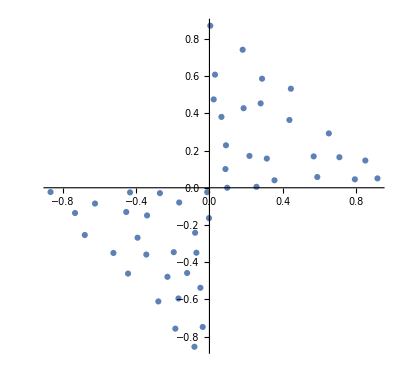

```mathematica
(* Creating list of initial Values *)
r=Random[];
listv0=Select[RandomReal[{-1,1},{1000,2}],(Sign[#[[1]]*#[[2]]]≥0 &&Abs[#[[1]]+#[[2]]]≤1)&];
listv0=Nest[removeClosest,listv0,Length[listv0]-50];
ListPlot[listv0,AspectRatio->Automatic]
```

## Little functions

```mathematica
affiche[{p_,v_},y_]:={RainbowColor[Rescale[v,{-2,2},{0,1}]],Point[{p-0.5,y+0.5}]};
```

```mathematica
RainbowColor[z_]:=Blend[{Purple,Blue,Cyan,Green,Yellow,Orange,Red},z];
```

```mathematica
bigTest[steps_,e_,minmaxList_,dis_]:=Block[{depth, resTable,realPVTable,pos,pv,g0},(
Table[
ic=move[ia,dis];
depth=stereoDepth[listv0,ia,ic,minmax[[2]],minmax,Range[1,103,steps],Range[1,45],e,"ConstrainedNewMethod"];

(* We only keep converged solutions *)
resTable=Table[
Select[depth[[r]],#[[2]]=="converged"&]
(*depth[[r]]*)
,{r,45}];

(* We give right coordinates to each solution *)
realPVTable=Table[
pos=resTable[[r,All,5]]-resTable[[r,All,3]];
pv=Thread[{pos,resTable[[r,All,1]]}]
,{r,45}];


(* We create g0 *)
g0=Graphics[{PointSize[0.009],Table[affiche[#,45-y]&/@realPVTable[[y]],{y,1,45}]}];
g0=Rasterize[Show[ia,g0],ImageSize->ImageDimensions[ia]*5,ImageResolution->300];

{realPVTable,g0}

,{minmax,minmaxList}]
)]
```

## Big Tests

```mathematica
e=0.0001;
```

#### Full image dis=0.3, step=1

```mathematica
dis=0.5;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
testList={{1,1}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

```mathematica
Subscript[resTable^step, dis][[1,1,row]]
```

{{1.5876,0.769633},{2.86347,0.304929},{3.73573,0.576397},{4.43846,0.906579},{6.22052,-0.967639},{6.8518,0.351755},{7.7936,0.445194},{8.74264,0.524178},{9.69929,0.566342},{11.8269,0.407008},{12.6807,0.658582},{13.9823,0.254478},{14.7347,0.566466},{15.5648,0.701484},{16.4987,0.676465},{17.8174,0.41491},{18.6596,0.704715},{19.0763,0.958464},{20.8574,0.335703},{21.7633,0.507723},{22.7504,0.486318},{23.7497,0.512038},{24.6136,0.743742},{25.8868,0.339015},{26.8137,0.400675},{27.7135,0.597274},{28.4569,0.78912},{29.8928,0.232722},{30.7515,0.559274},{32.8075,0.464386},{33.6854,0.600693},{35.8155,0.418371},{36.7553,0.508266},{38.7944,0.526745},{39.7406,0.474333},{40.6258,0.894783},{42.7858,-1.44151},{42.9167,0.271931},{43.6768,0.690962},{44.0673,0.970688},{45.86,0.355714},{46.7215,0.576625},{47.8135,0.36573},{48.82,0.402698},{49.6424,0.797816},{50.8689,0.389292},{51.6732,0.641047},{52.5698,0.5889},{53.7743,0.51343},{54.695,0.558344},{55.7962,0.417878},{57.7541,0.616544},{58.2362,0.953248},{60.0291,-0.0441392},{60.7469,0.584795},{61.5579,0.660957},{62.8101,0.416902},{63.9849,0.0929077},{64.821,0.405355},{65.7564,0.508605},{66.6895,0.58607},{67.6969,0.537029},{68.7808,0.454949},{69.6783,0.655521},{70.0036,1.02195},{71.6684,0.750955},{72.8997,0.300246},{73.8283,0.375632},{74.8052,0.420441},{75.7686,0.484419},{76.7516,0.49621},{77.7807,0.448284},{78.7709,0.477089},{79.752,0.501072},{80.7059,0.570318},{81.6479,0.612196},{82.659,0.599364},{83.5809,0.74432},{84.8839,0.348876},{85.8309,0.362846},{86.7897,0.454367},{87.7637,0.485151},{88.606,0.81507},{90.626,-1.12439},{90.8685,0.420597},{91.5859,0.76913},{92.9015,0.208405},{93.8269,0.39101},{94.7579,0.509701},{95.6939,0.577197},{96.5545,0.778305},{97.8726,0.351337},{98.7681,0.485046},{99.7416,0.513864},{100.773,0.453669},{101.767,0.492204},{102.73,0.505041}}

#### Line Test

```mathematica
row=5;
pyrfia=pyrFuncGen[ImageData[ia][[row]],4];
pyrfic=pyrFuncGen[ImageData[move[ia,dis]][[row]],4];
pyrfi=Flatten[{pyrfia,pyrfic},{{2},{1},{3}}];
```

```mathematica
resV=lineTest[listv0,Range[1,103],pyrfi[[1;;1]],e, "ConstrainedNewMethod"];

resV1=Select[resV,(#[[3]]=="converged")&][[All,1;;4]];
Thread[{resV1[[All,4]]-resV1[[All,1]],resV1[[All,1]]+resV1[[All,2]]}]
```

{{1.5876,0.769633},{2.86347,0.304929},{3.73573,0.576397},{4.43846,0.906579},{6.22052,-0.967639},{6.8518,0.351755},{7.7936,0.445194},{8.74264,0.524178},{9.69929,0.566342},{11.8269,0.407008},{12.6807,0.658582},{13.9823,0.254478},{14.7347,0.566466},{15.5648,0.701484},{16.4987,0.676465},{17.8174,0.41491},{18.6596,0.704715},{19.0763,0.958464},{20.8574,0.335703},{21.7633,0.507723},{22.7504,0.486318},{23.7497,0.512038},{24.6136,0.743742},{25.8868,0.339015},{26.8137,0.400675},{27.7135,0.597274},{28.4569,0.78912},{29.8928,0.232722},{30.7515,0.559274},{32.8075,0.464386},{33.6854,0.600693},{35.8155,0.418371},{36.7553,0.508266},{38.7944,0.526745},{39.7406,0.474333},{40.6258,0.894783},{42.7858,-1.44151},{42.9167,0.271931},{43.6768,0.690962},{44.0673,0.970688},{45.86,0.355714},{46.7215,0.576625},{47.8135,0.36573},{48.82,0.402698},{49.6424,0.797816},{50.8689,0.389292},{51.6732,0.641047},{52.5698,0.5889},{53.7743,0.51343},{54.695,0.558344},{55.7962,0.417878},{57.7541,0.616544},{58.2362,0.953248},{60.0291,-0.0441392},{60.7469,0.584795},{61.5579,0.660957},{62.8101,0.416902},{63.9849,0.0929077},{64.821,0.405355},{65.7564,0.508605},{66.6895,0.58607},{67.6969,0.537029},{68.7808,0.454949},{69.6783,0.655521},{70.0036,1.02195},{71.6684,0.750955},{72.8997,0.300246},{73.8283,0.375632},{74.8052,0.420441},{75.7686,0.484419},{76.7516,0.49621},{77.7807,0.448284},{78.7709,0.477089},{79.752,0.501072},{80.7059,0.570318},{81.6479,0.612196},{82.659,0.599364},{83.5809,0.74432},{84.8839,0.348876},{85.8309,0.362846},{86.7897,0.454367},{87.7637,0.485151},{88.606,0.81507},{90.626,-1.12439},{90.8685,0.420597},{91.5859,0.76913},{92.9015,0.208405},{93.8269,0.39101},{94.7579,0.509701},{95.6939,0.577197},{96.5545,0.778305},{97.8726,0.351337},{98.7681,0.485046},{99.7416,0.513864},{100.773,0.453669},{101.767,0.492204},{102.73,0.505041}}

#### Display Full image dis=0.3, step=1

```mathematica
dis=0.5;
step=1;
```

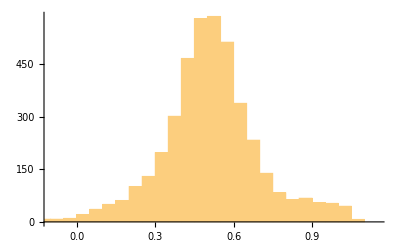

```mathematica
Histogram[Flatten[Subscript[resTable^step, dis][[1,1,All,All,2]]]]
```

```mathematica
wichShow=1;
g1=GraphicsRow[{GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]},ImageSize->500],BarLegend[{RainbowColor[#]&,{0,1}}]}]
```

-Graphics-

#### Little test

```mathematica
row=1;
pyrfia=pyrFuncGen[ImageData[ia][[row]],4];
pyrfic=pyrFuncGen[ImageData[move[ia,dis]][[row]],4];
pyrfi=Flatten[{pyrfia,pyrfic},{{2},{1},{3}}];
```

```mathematica
resV=lineTest[listv0,Range[1,103],pyrfi[[1;;4]],e, "ConstrainedNewMethod"];
resV1=Select[resV,(#[[3]]=="converged")&][[All,1;;4]];
Thread[{resV1[[All,4]]-resV1[[All,1]],resV1[[All,1]]+resV1[[All,2]]}]
```

{{0.743353,0.50918},{1.87684,0.333466},{2.73811,0.549548},{3.52432,0.879676},{5.75331,0.863822},{6.89271,0.333915},{7.82752,0.371558},{8.78642,0.460808},{9.74753,0.510406},{10.7336,0.517255},{11.8353,0.352633},{12.7884,0.463077},{13.6381,0.726371},{14.8911,0.336354},{15.7211,0.574528},{16.5739,0.683806},{17.6351,0.537672},{19.8145,0.552453},{21.6728,0.977642},{22.8533,0.453635},{23.6997,0.578193},{24.5324,0.825289},{25.9301,0.149114},{26.7664,0.525561},{27.8343,0.355905},{28.7374,0.571779},{29.5228,0.747944},{30.9031,0.23391},{31.759,0.538622},{32.6854,0.567523},{34.7911,0.519868},{36.7706,0.534667},{37.6757,0.570631},{38.759,0.482641},{39.6647,0.678032},{40.8692,0.244326},{41.788,0.481687},{42.6919,0.59089},{43.5904,0.658828},{44.8558,0.310924},{45.79,0.464901},{46.7236,0.548095},{47.6189,0.690907},{48.8698,0.249483},{49.7666,0.530311},{50.7677,0.442251},{51.7723,0.487017},{52.6523,0.662851},{53.8551,0.28084},{54.7621,0.540032},{55.6305,0.633866},{56.7729,0.421659},{57.7182,0.609498},{58.6798,0.496225},{59.8617,0.336647},{60.7728,0.489536},{61.7331,0.521218},{62.7684,0.465155},{63.7725,0.471224},{64.7712,0.470226},{65.8032,0.420484},{66.7741,0.477549},{67.7316,0.532987},{68.7114,0.545155},{69.6665,0.622276},{70.5866,0.629447},{71.8155,0.399335},{72.6417,0.822616},{74.9038,0.347906},{75.6326,0.83478},{76.837,0.5992},{78.8702,0.314451},{79.7803,0.47958},{80.6991,0.579361},{81.6547,0.597974},{82.5901,0.846345},{83.8282,0.510317},{84.7749,0.416474},{85.8644,0.304261},{86.8071,0.433971},{87.7029,0.600786},{88.5216,0.72716},{89.8718,0.287862},{90.7194,0.624854},{91.8258,0.320553},{92.8503,0.359876},{93.7665,0.498973},{94.7097,0.555383},{95.7031,0.549114},{96.7006,0.569378},{98.8456,0.370767},{99.787,0.452827},{100.77,0.473974},{101.757,0.496106},{102.739,0.513447}}

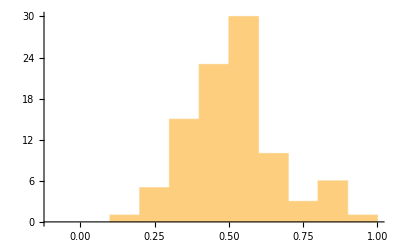

```mathematica
Histogram[resV1[[All,1]]+resV1[[All,2]]]
```

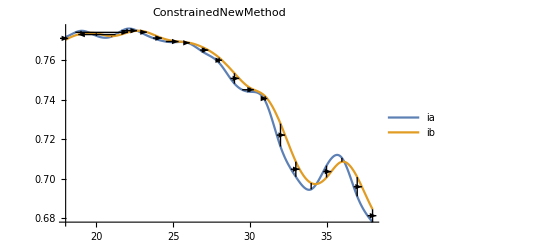

```mathematica
seeAllLine[listv0,Range[18,38],pyrfi[[1;;4]],e, "ConstrainedNewMethod"]
```

#### Full image dis=0.5, step=0.5

```mathematica
dis=0.5;
step=0.5;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=0.5, step=0.5

```mathematica
dis=0.5;
step=0.5;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

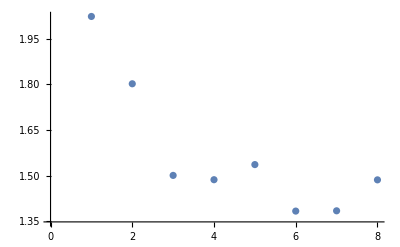

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=3;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=0.1, step=1

```mathematica
dis=0.1;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=0.1, step=1

```mathematica
dis=0.1;
step=1;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

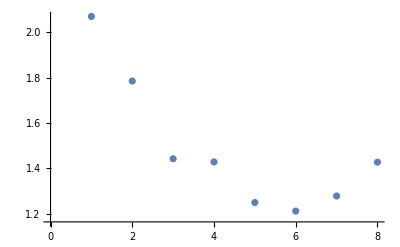

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=1.5, step=1

```mathematica
dis=1.5;
step=1;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=1.5, step=1

```mathematica
dis=1.5;
step=1;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

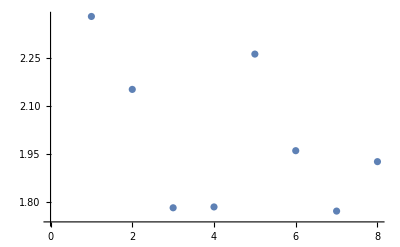

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-

#### Full image dis=1.5, step=0.2

```mathematica
dis=1.5;
step=0.2;
```

```mathematica
testList={{1,1},{1,2},{1,3},{1,4},{4,4},{3,4},{2,4},{1,4}};
Subscript[resTable^step, dis]=bigTest[step,e,testList,dis];
```

#### Display Full image dis=1.5, step=0.2

```mathematica
dis=1.5;
step=0.2;
```

```mathematica
densityValues=Table[

p=DeleteDuplicates/@Round[res[[All,All,1]]-0.5];
pxy=Table[Thread[{r,p[[r]]}],{r,Length[p]}];
density=103.*45./Length[Flatten[pxy,1]];
rmse=Sqrt[Mean[(Flatten[res,1][[All,2]]-dis)^2]];

{density,rmse}

,{res, Subscript[resTable^step, dis][[All,1]]}];
```

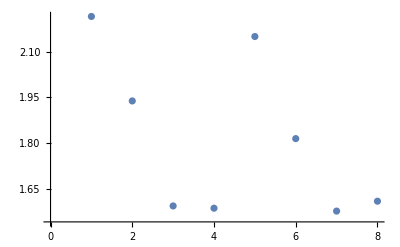

```mathematica
ListPlot[Sqrt[Total/@densityValues^2]]
```

```mathematica
wichShow=6;
g1=GraphicsColumn[{Subscript[resTable^step, dis][[wichShow,2]],testList[[wichShow]]}]
```

-Graphics-